# Celoštevilsko linearno programiranje

Primer Gomoryjeve metode

#### Podatki

```mathematica
c={0,1,0};
m={{1,2,3},{3,5,6}};
b={4,11};
```

```mathematica
b0=Partition[Join[Riffle[b,0],{0}],2]
```

{{4,0},{11,0}}

#### Celoštevilska optimalna rešitev

```mathematica
ilp=LinearProgramming[c,m,b0,Automatic,Integers]
c.ilp
```

LinearProgramming::lpip: Warning: integer linear programming will use a machine-precision approximation of the inputs.

{2,1,0}

1

#### Realna rešitev

```mathematica
lp=LinearProgramming[c,m,b0]
```

{3,0,1/3}

```mathematica
c.lp
```

0

```mathematica
dp=LinearProgramming[-b,-Transpose[m],-c]
```

{0,0}

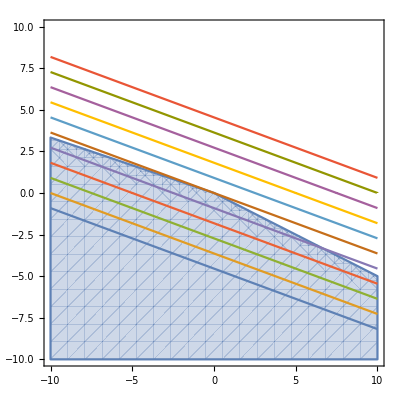

```mathematica
d=10;
Show[
RegionPlot[{Apply[And,Thread[Transpose[m].{Subscript[y, 1],Subscript[y, 2]}≤ c]]},{Subscript[y, 1],-d,d},{Subscript[y, 2],-d,d}],
ContourPlot[Evaluate[Table[b.{Subscript[y, 1],Subscript[y, 2]}== c,{c,-50,50,10}]],{Subscript[y, 1],-d,d},{Subscript[y, 2],-d,d}]]
```

## Reševanje po Gomoryju

#### Realni LP

```mathematica
lp=LinearProgramming[c,m,b0]
c.lp
```

{3,0,1/3}

0

Sestavimo bazično matriko in izračunamo njen inverz

```mathematica
m0 ={{1,3},{3,6}};
m1=Inverse[m0].m;
%//MatrixForm
b1=Inverse[m0].b
```

(1 | 1 | 0
0 | 1/3 | 1)

{3,1/3}

```mathematica
CongruenceMy[x_] := x - Floor[x]
```

Matriki dodamo kongruenčne vezi

```mathematica
CongruenceMy[m1]//MatrixForm
```

(0 | 0 | 0
0 | 1/3 | 0)

```mathematica
m2=Join[m,CongruenceMy[m1]];
%//MatrixForm
```

(1 | 2 | 3
3 | 5 | 6
0 | 0 | 0
0 | 1/3 | 0)

```mathematica
b2 = Join[b,CongruenceMy[b1]]
```

{4,11,0,1/3}

```mathematica
m2=Delete[m2,3]
```

{{1,2,3},{3,5,6},{0,1/3,0}}

```mathematica
b2=Delete[b2,3]
```

{4,11,1/3}

Dodamo novi spremenljivki

```mathematica
m2 =Transpose[Join[{{0,0,-1}},Transpose[m2]]];
%//MatrixForm
```

(0 | 1 | 2 | 3
0 | 3 | 5 | 6
-1 | 0 | 1/3 | 0)

Razširimo še vektor c

```mathematica
c2 = Join[{0},c]
```

{0,0,1,0}

Rešimo razširjen LP v realnem

```mathematica
b20=Partition[Join[Riffle[b2,0],{0}],2]
lp2=LinearProgramming[c2,m2,b20]
```

{{4,0},{11,0},{1/3,0}}

{0,2,1,0}

Dobili smo optimalno celoštevilčno rešitev. Rešitev je

```mathematica
lp2[[1;;4]]
```

{0,2,1,0}

#### Kontrola

```mathematica
c2.lp2[[1;;4]]
m2.lp2[[1;;4]]-b2
```

1

{0,0,0}

Še en primer Gomoryjeve metode

#### Podatki

```mathematica
c={1,2,3};
m={{1,2,3},{4,5,6}};
b={68,167};
```

```mathematica
b0=Partition[Join[Riffle[b,0],{0}],2]
```

{{68,0},{167,0}}

#### Celoštevilska optimalna rešitev

```mathematica
ilp=LinearProgramming[c,m,b0,Automatic,Integers]
c.ilp
```

LinearProgramming::lpip: Warning: integer linear programming will use a machine-precision approximation of the inputs.

{15,1,17}

68

### Reševanje po Gomoryju step by step

#### Realni LP

```mathematica
lp=LinearProgramming[c,m,b0]
c.lp
```

{31/2,0,35/2}

68

Sestavimo bazično matriko in izračunamo njen inverz

```mathematica
m0 ={{1,3},{4,6}};
m1=Inverse[m0].m;
%//MatrixForm
b1=Inverse[m0].b
```

(1 | 1/2 | 0
0 | 1/2 | 1)

{31/2,35/2}

```mathematica
CongruenceMy[x_] := x - Floor[x]
```

Matriki dodamo kongruenčne vezi

```mathematica
m2=Join[m,{First[CongruenceMy[m1]]}];
%//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
0 | 1/2 | 0)

```mathematica
b2 = Join[b,{First[CongruenceMy[b1]]}]
```

{68,167,1/2}

Dodamo novi spremenljivki

```mathematica
m2 =Transpose[Join[{{0,0,1}},Transpose[m2]]];
%//MatrixForm
```

(0 | 1 | 2 | 3
0 | 4 | 5 | 6
1 | 0 | 1/2 | 0)

Razširimo še vektor c

```mathematica
c2 = Join[{0},c]
```

{0,1,2,3}

Rešimo razširjen LP v realnem

```mathematica
lp2=LinearProgramming[c2,m2,Partition[Riffle[b2,Table[0,{Length[b2]}]],2]]
```

{0,15,1,17}

Dobili smo optimalno celoštevilčno rešitev. Rešitev je

```mathematica
lp2[[2;;4]]
```

{15,1,17}

#### Kontrola

```mathematica
c.lp2[[2;;4]]
m.lp2[[2;;4]]-b
```

68

{0,0}

### Reševanje z ukazom GomoryjStep

```mathematica
GomoryStep[c_,a_,b_]:= Module[{n,m,lp,l1,l2,a0,a1,b1,i1,a2,b2,c2,b20,lp2},
n=Length[c];
m=Length[b];
lp=LinearProgramming[c,a,Partition[Riffle[b,Table[0,Length[b]]],2]];
If[AllTrue[lp, IntegerQ],{lp},
(l1=Map[First,Position[lp,0]];
         l2=Partition[Complement[Table[i,{i,n}],l1],1];
a0 =Table[Extract[a[[i]],l2],{i,Length[a]}];
a1=Inverse[a0].a;
b1=Inverse[a0].b;
i1=First[Position[Map[IntegerQ,CongruenceMy[b1]],False]][[1]];
a2=Join[a,{CongruenceMy[a1][[i1]]}];
b2 = Join[b,{CongruenceMy[b1][[i1]]}];
a2 =Transpose[Join[{Join[Table[0,{m}],{-1}]},Transpose[a2]]];
c2 = Join[{0},c];
{c2,a2,b2})]
]
```

Prvi korak

```mathematica
gs1=GomoryStep[c,m,b]
```

{{0,1,2,3},{{0,1,2,3},{0,4,5,6},{-1,0,1/2,0}},{68,167,1/2}}

Drugi korak

```mathematica
gs2=Apply[GomoryStep,gs1]
```

{{15,0,31,2}}

Rešitev je

```mathematica
gs=Take[gs2[[1]],-Length[c]]
```

{0,31,2}

Kontrola

```mathematica
m.gs-b
```

{0,0}

```mathematica
c.gs
```

68

Enaka optimalna vrednost, pri drugi dopustni rešitvi.

Še en primer Gomoryjeve metode

#### Podatki

```mathematica
n=3;
m=2;
```

```mathematica
c = Table[RandomInteger[{1,10}],n]
```

{7,2,10}

```mathematica
a = Table[RandomInteger[{1,10}],{m},{n}]
```

{{3,3,10},{4,3,3}}

```mathematica
MatrixRank[a]
```

2

```mathematica
x = Table[RandomInteger[{1,10}],n]
```

{9,5,5}

```mathematica
b = a.x
```

{92,66}

#### Celoštevilska optimalna rešitev

```mathematica
b0=Partition[Riffle[b,Table[0,m]],2]
```

{{92,0},{66,0}}

```mathematica
ilp=LinearProgramming[c,a,b0,Automatic,Integers]
c.ilp
```

LinearProgramming::lpip: Warning: integer linear programming will use a machine-precision approximation of the inputs.

{9,5,5}

123

### Reševanje po Gomoryju

```mathematica
gs1=GomoryStep[c,a,b]
```

{{0,7,2,10},{{0,3,3,10},{0,4,3,3},{-1,10/21,0,0}},{92,66,2/7}}

```mathematica
gs2=Apply[GomoryStep,gs1]
```

{{0,0,7,2,10},{{0,0,3,3,10},{0,0,4,3,3},{0,-1,10/21,0,0},{-1,9/10,0,0,0}},{92,66,2/7,3/5}}

```mathematica
gs3=Apply[GomoryStep,gs2]
```

{{0,0,0,7,2,10},{{0,0,0,3,3,10},{0,0,0,4,3,3},{0,0,-1,10/21,0,0},{0,-1,9/10,0,0,0},{-1,8/9,0,0,0,0}},{92,66,2/7,3/5,2/3}}

```mathematica
gs4=Apply[GomoryStep,gs3]
```

{{0,0,0,0,7,2,10},{{0,0,0,0,3,3,10},{0,0,0,0,4,3,3},{0,0,0,-1,10/21,0,0},{0,0,-1,9/10,0,0,0},{0,-1,8/9,0,0,0,0},{-1,7/8,0,0,0,0,0}},{92,66,2/7,3/5,2/3,3/4}}

```mathematica
gs5=Apply[GomoryStep,gs4]
```

{{0,0,0,0,0,7,2,10},{{0,0,0,0,0,3,3,10},{0,0,0,0,0,4,3,3},{0,0,0,0,-1,10/21,0,0},{0,0,0,-1,9/10,0,0,0},{0,0,-1,8/9,0,0,0,0},{0,-1,7/8,0,0,0,0,0},{-1,6/7,0,0,0,0,0,0}},{92,66,2/7,3/5,2/3,3/4,6/7}}

```mathematica
gs6=Apply[GomoryStep,gs5]
```

{{0,1,2,3,4,9,5,5}}

```mathematica
gs=Take[gs6[[1]],-Length[c]]
```

{9,5,5}

```mathematica
a.gs-b
```

{0,0}

```mathematica
c.gs
```

123

Še en primer Gomoryjeve metode

#### Podatki

```mathematica
n=4;
m=3;
```

```mathematica
c = Table[RandomInteger[{1,10}],n]
```

{1,5,9,1}

```mathematica
a = Table[RandomInteger[{1,10}],{m},{n}]
```

{{1,6,2,4},{10,1,8,5},{7,8,4,9}}

```mathematica
MatrixRank[a]
```

3

```mathematica
x = Table[RandomInteger[{1,10}],n]
```

{1,1,7,6}

```mathematica
b = a.x
```

{45,97,97}

#### Celoštevilska optimalna rešitev

```mathematica
b0=Partition[Riffle[b,Table[0,m]],2]
```

{{45,0},{97,0},{97,0}}

```mathematica
ilp=LinearProgramming[c,a,b0,Automatic,Integers]
c.ilp
```

LinearProgramming::lpip: Warning: integer linear programming will use a machine-precision approximation of the inputs.

{1,1,7,6}

75

### Reševanje po Gomoryju

```mathematica
gs1=GomoryStep[c,a,b]
```

{{0,1,5,9,1},{{0,1,6,2,4},{0,10,1,8,5},{0,7,8,4,9},{-1,0,0,0,67/91}},{45,97,97,38/91}}

```mathematica
gs2=Apply[GomoryStep,gs1]
```

{{0,0,1,5,9,1},{{0,0,1,6,2,4},{0,0,10,1,8,5},{0,0,7,8,4,9},{0,-1,0,0,0,67/91},{-1,61/67,0,0,0,0}},{45,97,97,38/91,43/67}}

```mathematica
gs3=Apply[GomoryStep,gs2]
```

{{0,0,0,1,5,9,1},{{0,0,0,1,6,2,4},{0,0,0,10,1,8,5},{0,0,0,7,8,4,9},{0,0,-1,0,0,0,67/91},{0,-1,61/67,0,0,0,0},{-1,55/61,0,0,0,0,0}},{45,97,97,38/91,43/67,43/61}}

```mathematica
gs4=Apply[GomoryStep,gs3]
```

{{0,0,0,0,1,5,9,1},{{0,0,0,0,1,6,2,4},{0,0,0,0,10,1,8,5},{0,0,0,0,7,8,4,9},{0,0,0,-1,0,0,0,67/91},{0,0,-1,61/67,0,0,0,0},{0,-1,55/61,0,0,0,0,0},{-1,49/55,0,0,0,0,0,0}},{45,97,97,38/91,43/67,43/61,43/55}}

```mathematica
gs5=Apply[GomoryStep,gs4]
```

{{0,0,0,0,0,1,5,9,1},{{0,0,0,0,0,1,6,2,4},{0,0,0,0,0,10,1,8,5},{0,0,0,0,0,7,8,4,9},{0,0,0,0,-1,0,0,0,67/91},{0,0,0,-1,61/67,0,0,0,0},{0,0,-1,55/61,0,0,0,0,0},{0,-1,49/55,0,0,0,0,0,0},{-1,43/49,0,0,0,0,0,0,0}},{45,97,97,38/91,43/67,43/61,43/55,43/49}}

```mathematica
gs6=Apply[GomoryStep,gs5]
```

{{0,1,2,3,4,1,1,7,6}}

```mathematica
gs=Take[gs6[[1]],-Length[c]]
```

{1,1,7,6}

```mathematica
a.gs-b
```

{0,0}

```mathematica
c.gs
```

122

```mathematica
gs0=GomoryStep[c,a,b];
flag = True; ns=0;
While[flag,ns++;gs0=Apply[GomoryStep,gs0];flag=(Length[gs0]> 1 && ns< 100)]
Take[gs6[[1]],-Length[c]]
```

{1,1,7,6}

Še en primer Gomoryjeve metode

#### Podatki

```mathematica
n=5;
m=4;
```

```mathematica
c = Table[RandomInteger[{1,10}],n]
```

{5,7,2,6,9}

```mathematica
a = Table[RandomInteger[{1,10}],{m},{n}]
```

{{10,1,1,4,4},{10,5,8,5,8},{1,1,2,9,4},{5,3,1,4,6}}

```mathematica
MatrixRank[a]
```

4

```mathematica
x = Table[RandomInteger[{1,10}],n]
```

{9,4,8,4,4}

```mathematica
b = a.x
```

{134,226,81,105}

#### Celoštevilska optimalna rešitev

```mathematica
b0=Partition[Riffle[b,Table[0,m]],2]
```

{{134,0},{226,0},{81,0},{105,0}}

```mathematica
ilp=LinearProgramming[c,a,b0,Automatic,Integers]
c.ilp
```

LinearProgramming::lpip: Warning: integer linear programming will use a machine-precision approximation of the inputs.

{9,4,8,4,4}

149

### Reševanje po Gomoryju

```mathematica
gs0=GomoryStep[c,a,b];
flag = True; ns=0;
While[flag,ns++;gs0=Apply[GomoryStep,gs0];flag=(Length[gs0]> 1 && ns< 100)]
Take[gs0[[1]],-Length[c]]
```

{9,4,8,4,4}